```mathematica
<<QINisq`
gghz[a_,b_]:={a,0,0,0,0,0,0,b};
gw[c_,d_,e_]:={0,c,d,0,e,0,0,0};
gsw[f_,g_,h_]:={0,0,0,f,0,g,h,0};
GME[ρ_,partitions_]:=√(2(1-Tr[MatrixPower[PartialTrace[ρ,{2,2,2},partitions],2]]));
τ3[ψ_]:=Module[{d1,d2,d3},
d1=ψ[[1]]^2 ψ[[8]]^2+ψ[[2]]^2 ψ[[7]]^2+ψ[[3]]^2 ψ[[6]]^2+ψ[[4]]^2 ψ[[5]]^2;
d2=ψ[[1]]ψ[[8]]ψ[[4]]ψ[[5]]+ψ[[1]]ψ[[8]]ψ[[3]]ψ[[6]]+ψ[[1]]ψ[[8]]ψ[[2]]ψ[[7]]+ψ[[4]]ψ[[5]]ψ[[3]]ψ[[6]]+ψ[[4]]ψ[[5]]ψ[[2]]ψ[[7]]+ψ[[3]]ψ[[6]]ψ[[2]]ψ[[7]];
d3=ψ[[1]]ψ[[7]]ψ[[6]]ψ[[4]]+ψ[[8]]ψ[[2]]ψ[[3]]ψ[[5]];
Return[4Abs[d1-2d2+4d3]];
];
indexToQubitIndices[n_,numQubits_]:=PadLeft[IntegerDigits[n-1,2],numQubits];
permutationMatrix[permutation_]:=With[{numQubits=Length@permutation},SparseArray[{{i_,j_}:>1/;Equal[Permute[indexToQubitIndices[i,numQubits],permutation],indexToQubitIndices[j,numQubits]]},2^numQubits {1,1}]];
M[i_]:=Switch[i,1,permutationMatrix[{4,2,3,1,5,6}],2,permutationMatrix[{1,5,3,4,2,6}],3,permutationMatrix[{1,2,6,4,5,3}]];
```

Package QI version 0.4.40 (last modification: 22/01/2023).

Package QIExtras 0.0.14 (last modification: 27/08/2023).

Package QINisq 0.0.13 (last modification: 18/10/2023).

## 1 Localized State

```mathematica
$Assumptions=0<=a<=1/(√2)∧0<ϕ<=2π∧0<=p<=1
ψ[p_,a_,ϕ_]:=√p gw[a,-√(1-2 a^2),a]+√(1-p) ⅇ^(ⅈ ϕ)gghz[1,0];
```

0≤a≤1/(√2)&&0<ϕ≤2 π&&0≤p≤1

```mathematica
Ψ=ψ[p,a,ϕ]
ρ=FullSimplify[Outer[Times,Ψ*,Ψ]]
eq1=FullSimplify[GME[ρ,{1,2}]]
eq2=FullSimplify[GME[ρ,{1,3}]]
```

{ⅇ^(ⅈ ϕ) √(1-p),a √p,-√(1-2 a^2) √p,0,a √p,0,0,0}

(1-p | a ⅇ^(-ⅈ ϕ) √((1-p) p) | -ⅇ^(-ⅈ ϕ) √((-1+2 a^2) (-1+p) p) | 0 | a ⅇ^(-ⅈ ϕ) √((1-p) p) | 0 | 0 | 0
a ⅇ^(ⅈ ϕ) √((1-p) p) | a^2 p | -a √(1-2 a^2) p | 0 | a^2 p | 0 | 0 | 0
-ⅇ^(ⅈ ϕ) √((-1+2 a^2) (-1+p) p) | -a √(1-2 a^2) p | p-2 a^2 p | 0 | -a √(1-2 a^2) p | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
a ⅇ^(ⅈ ϕ) √((1-p) p) | a^2 p | -a √(1-2 a^2) p | 0 | a^2 p | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

2 a √(1-a^2) p

2 a √(2-4 a^2) p

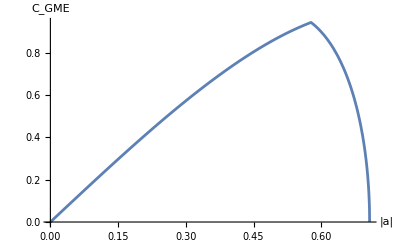

```mathematica
Plot[Min[{eq1,eq2}]/.p->1,{a,0,1/(√2)},AxesLabel->{"|a|",Subscript[C, GME]}]
```

## 2 Localized States

```mathematica
$Assumptions=0<=a<=1/(√2)∧0<=b<=1/(√2)∧0<=ϕ1<2π∧0<=ϕ2<2π∧0<=ϕ3<2π∧0<=ϕ4<2π∧0<=p<=1∧0<=q<=1∧0<=r<=1∧0<=s<=1∧0<=p+q+r+s<=1
ψ[p_,q_,r_,s_,a_,b_,ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=√p gw[a,√(1-2 a^2),a]+√q ⅇ^(ⅈ ϕ1)gw[1/(√2),0,-1/(√2)]+√r ⅇ^(ⅈ ϕ2)gw[√((1-2 a^2)/2),-(2a)/(√2),√((1-2 a^2)/2)]+√s ⅇ^(ⅈ ϕ3)gsw[b,√(1-2 b^2),b] +√(1-p-q-r-s)ⅇ^(ⅈ ϕ4)gghz[1,0];
```

0≤a≤1/(√2)&&0≤b≤1/(√2)&&0≤ϕ1<2 π&&0≤ϕ2<2 π&&0≤ϕ3<2 π&&0≤ϕ4<2 π&&0≤p≤1&&0≤q≤1&&0≤r≤1&&0≤s≤1&&0≤p+q+r+s≤1

```mathematica
Ψ=ψ[p,0,r,s,a,b,ϕ1,ϕ2,ϕ3,ϕ4]
ρ=FullSimplify[Outer[Times,Ψ*,Ψ]]
eq1=(GME[ρ,{1,2}]/2)^2/.{Conjugate[ⅇ^(ⅈ ϕ1) √q+ⅇ^(ⅈ ϕ2) √(r-2 a^2 r)]->ⅇ^(ⅈ -ϕ1) √q+ⅇ^(ⅈ -ϕ2) √(r-2 a^2 r),Conjugate[-ⅇ^(ⅈ ϕ1) √q+ⅇ^(ⅈ ϕ2) √(r-2 a^2 r)]->-ⅇ^(-ⅈ ϕ1) √q+ⅇ^(-ⅈ ϕ2) √(r-2 a^2 r)}//FullSimplify
eq2=(GME[ρ,{1,3}]/2)^2/.{Conjugate[ⅇ^(ⅈ ϕ1) √q+ⅇ^(ⅈ ϕ2) √(r-2 a^2 r)]->ⅇ^(ⅈ -ϕ1) √q+ⅇ^(ⅈ -ϕ2) √(r-2 a^2 r),Conjugate[-ⅇ^(ⅈ ϕ1) √q+ⅇ^(ⅈ ϕ2) √(r-2 a^2 r)]->-ⅇ^(-ⅈ ϕ1) √q+ⅇ^(-ⅈ ϕ2) √(r-2 a^2 r)}//FullSimplify
```

{ⅇ^(ⅈ ϕ4) √(1-p-r-s),a √p+(√(1-2 a^2) ⅇ^(ⅈ ϕ2) √r)/(√2),√(1-2 a^2) √p-√2 a ⅇ^(ⅈ ϕ2) √r,b ⅇ^(ⅈ ϕ3) √s,a √p+(√(1-2 a^2) ⅇ^(ⅈ ϕ2) √r)/(√2),√(1-2 b^2) ⅇ^(ⅈ ϕ3) √s,b ⅇ^(ⅈ ϕ3) √s,0}

(1-p-r-s | 1/2 ⅇ^(-ⅈ ϕ4) (2 a √p+√2 ⅇ^(ⅈ ϕ2) √(r-2 a^2 r)) √(1-p-r-s) | ⅇ^(-ⅈ ϕ4) (√(p-2 a^2 p)-√2 a ⅇ^(ⅈ ϕ2) √r) √(1-p-r-s) | b ⅇ^(ⅈ (ϕ3-ϕ4)) √(-s (-1+p+r+s)) | 1/2 ⅇ^(-ⅈ ϕ4) (2 a √p+√2 ⅇ^(ⅈ ϕ2) √(r-2 a^2 r)) √(1-p-r-s) | ⅇ^(ⅈ (ϕ3-ϕ4)) √((-1+2 b^2) s (-1+p+r+s)) | b ⅇ^(ⅈ (ϕ3-ϕ4)) √(-s (-1+p+r+s)) | 0
ⅇ^(ⅈ ϕ4) (a √p+(ⅇ^(-ⅈ ϕ2) √(r-2 a^2 r))/(√2)) √(1-p-r-s) | a^2 (p-r)+r/2+√2 a √((1-2 a^2) p r) Cos[ϕ2] | (√(p-2 a^2 p)-√2 a ⅇ^(ⅈ ϕ2) √r) (a √p+(ⅇ^(-ⅈ ϕ2) √(r-2 a^2 r))/(√2)) | b ⅇ^(ⅈ ϕ3) (a √p+(ⅇ^(-ⅈ ϕ2) √(r-2 a^2 r))/(√2)) √s | a^2 (p-r)+r/2+√2 a √((1-2 a^2) p r) Cos[ϕ2] | ⅇ^(ⅈ ϕ3) (a √p+(ⅇ^(-ⅈ ϕ2) √(r-2 a^2 r))/(√2)) √(s-2 b^2 s) | b ⅇ^(ⅈ ϕ3) (a √p+(ⅇ^(-ⅈ ϕ2) √(r-2 a^2 r))/(√2)) √s | 0
ⅇ^(ⅈ ϕ4) (√(p-2 a^2 p)-√2 a ⅇ^(-ⅈ ϕ2) √r) √(1-p-r-s) | 1/2 (√(p-2 a^2 p)-√2 a ⅇ^(-ⅈ ϕ2) √r) (2 a √p+√2 ⅇ^(ⅈ ϕ2) √(r-2 a^2 r)) | p-2 a^2 p+2 a^2 r-2 √2 a √((1-2 a^2) p r) Cos[ϕ2] | b ⅇ^(ⅈ ϕ3) (√(p-2 a^2 p)-√2 a ⅇ^(-ⅈ ϕ2) √r) √s | 1/2 (√(p-2 a^2 p)-√2 a ⅇ^(-ⅈ ϕ2) √r) (2 a √p+√2 ⅇ^(ⅈ ϕ2) √(r-2 a^2 r)) | ⅇ^(ⅈ ϕ3) (√(p-2 a^2 p)-√2 a ⅇ^(-ⅈ ϕ2) √r) √(s-2 b^2 s) | b ⅇ^(ⅈ ϕ3) (√(p-2 a^2 p)-√2 a ⅇ^(-ⅈ ϕ2) √r) √s | 0
b ⅇ^(-ⅈ (ϕ3-ϕ4)) √(-s (-1+p+r+s)) | 1/2 b ⅇ^(-ⅈ ϕ3) (2 a √p+√2 ⅇ^(ⅈ ϕ2) √(r-2 a^2 r)) √s | b ⅇ^(-ⅈ ϕ3) (√((1-2 a^2) p s)-√2 a ⅇ^(ⅈ ϕ2) √(r s)) | b^2 s | 1/2 b ⅇ^(-ⅈ ϕ3) (2 a √p+√2 ⅇ^(ⅈ ϕ2) √(r-2 a^2 r)) √s | b √(1-2 b^2) s | b^2 s | 0
ⅇ^(ⅈ ϕ4) (a √p+(ⅇ^(-ⅈ ϕ2) √(r-2 a^2 r))/(√2)) √(1-p-r-s) | a^2 (p-r)+r/2+√2 a √((1-2 a^2) p r) Cos[ϕ2] | (√(p-2 a^2 p)-√2 a ⅇ^(ⅈ ϕ2) √r) (a √p+(ⅇ^(-ⅈ ϕ2) √(r-2 a^2 r))/(√2)) | b ⅇ^(ⅈ ϕ3) (a √p+(ⅇ^(-ⅈ ϕ2) √(r-2 a^2 r))/(√2)) √s | a^2 (p-r)+r/2+√2 a √((1-2 a^2) p r) Cos[ϕ2] | ⅇ^(ⅈ ϕ3) (a √p+(ⅇ^(-ⅈ ϕ2) √(r-2 a^2 r))/(√2)) √(s-2 b^2 s) | b ⅇ^(ⅈ ϕ3) (a √p+(ⅇ^(-ⅈ ϕ2) √(r-2 a^2 r))/(√2)) √s | 0
ⅇ^(-ⅈ (ϕ3-ϕ4)) √((-1+2 b^2) s (-1+p+r+s)) | 1/2 ⅇ^(-ⅈ ϕ3) (2 a √p+√2 ⅇ^(ⅈ ϕ2) √(r-2 a^2 r)) √(s-2 b^2 s) | ⅇ^(-ⅈ ϕ3) (√(p-2 a^2 p)-√2 a ⅇ^(ⅈ ϕ2) √r) √(s-2 b^2 s) | b √(1-2 b^2) s | 1/2 ⅇ^(-ⅈ ϕ3) (2 a √p+√2 ⅇ^(ⅈ ϕ2) √(r-2 a^2 r)) √(s-2 b^2 s) | s-2 b^2 s | b √(1-2 b^2) s | 0
b ⅇ^(-ⅈ (ϕ3-ϕ4)) √(-s (-1+p+r+s)) | 1/2 b ⅇ^(-ⅈ ϕ3) (2 a √p+√2 ⅇ^(ⅈ ϕ2) √(r-2 a^2 r)) √s | b ⅇ^(-ⅈ ϕ3) (√((1-2 a^2) p s)-√2 a ⅇ^(ⅈ ϕ2) √(r s)) | b^2 s | 1/2 b ⅇ^(-ⅈ ϕ3) (2 a √p+√2 ⅇ^(ⅈ ϕ2) √(r-2 a^2 r)) √s | b √(1-2 b^2) s | b^2 s | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

1/2 (1-2 (1/2 ⅇ^(-ⅈ ϕ4) (2 a √p+√2 ⅇ^(ⅈ ϕ2) √(r-2 a^2 r)) √(1-p-r-s)+b ⅇ^(ⅈ ϕ3) (√(p-2 a^2 p)-√2 a ⅇ^(-ⅈ ϕ2) √r) √s+ⅇ^(ⅈ ϕ3) (a √p+(ⅇ^(-ⅈ ϕ2) √(r-2 a^2 r))/(√2)) √(s-2 b^2 s)) (ⅇ^(ⅈ ϕ4) (a √p+(ⅇ^(-ⅈ ϕ2) √(r-2 a^2 r))/(√2)) √(1-p-r-s)+1/2 ⅇ^(-ⅈ ϕ3) (2 a √p+√2 ⅇ^(ⅈ ϕ2) √(r-2 a^2 r)) √(s-2 b^2 s)+b ⅇ^(-ⅈ ϕ3) (√((1-2 a^2) p s)-√2 a ⅇ^(ⅈ ϕ2) √(r s)))-(a^2 (p-r)+r/2+s-b^2 s+√2 a √((1-2 a^2) p r) Cos[ϕ2])^2-1/4 (-2+2 a^2 (p-r)+r+2 s-2 b^2 s+2 √2 a √((1-2 a^2) p r) Cos[ϕ2])^2)

-4 a^4 (p-r)^2+p (r+s-4 b^2 s)-2 b^2 s (-1+r+2 b^2 s)+2 a^2 (p-r) (p-r+(-1+2 b^2) s)-2 √2 a (√((1-2 a^2) p^3 r)+√((1-2 a^2) p r^3)+√((1-2 a^2) p r) ((-2+4 a^2) p-4 a^2 r+s-2 b^2 s)) Cos[ϕ2]+8 a^2 (-1+2 a^2) p r Cos[ϕ2]^2+2 √2 (-1+4 a^2) b √(-p r s (-1+p+r+s)) Cos[ϕ2-ϕ3-ϕ4]+4 a b √((-1+2 a^2) s (-1+p+r+s)) (r Cos[2 ϕ2-ϕ3-ϕ4]-p Cos[ϕ3+ϕ4])

```mathematica
eq11=eq1/.{ϕ->π,ϕ1->0}//FullSimplify (*Assuming q >= p*)
```

```mathematica
eq11=eq1/.{q->0,r->1-p}//FullSimplify
```

-a^4+1/4 (-1+p)^2+a^2 p

```mathematica
D[%,p]//FullSimplify
```

a^2+1/2 (-1+p)

```mathematica
eq22=eq2/.{ϕ->π,q->0,r->1-p}//FullSimplify
```

-2 a^2 (-1+2 a^2) (1+(-1+p) p)

```mathematica
Plot3D[Min[eq11,eq22],{a,0,1/(√2)},{p,0,1},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Manipulate[Plot[Max[0,Min[eq11,eq22]]/.{a->a1,p->p1},{p1,0,1},PlotRange->{0,0.25}],{a1,0,1/(√2)}]
```

```mathematica
D[%,p]//FullSimplify
```

-2 a^2 (-1+2 a^2) (-1+2 p)

```mathematica
sol1=Reduce[eq11==0∧0<a<1/(√2)∧0<=p<=1∧0<=q<=1∧0<=r<=1∧0<=p+q+r<=1,{p,q,r},Reals]
```

False

```mathematica
sol2=Reduce[eq22==0∧0<a<1/(√2)∧0<=p<=1∧0<=q<=1∧0<=r<=1∧0<=p+q+r<=1,{p,q,r},Reals]
```

$Aborted

## 3 Localized States d -> ∞?

```mathematica
$Assumptions=0<=ϕ1<2π∧0<=ϕ2<2π∧0<=ϕ3<2π∧0<=ϕ4<2π∧0<=ϕ5<2π∧0<=ϕ6<2π∧0<=ϕ7<2π∧0<=p<=1∧0<=q<=1∧0<=r<=1∧0<=s<=1∧0<=t<=1∧0<=u<=1∧0<=v<=1∧0<=p+q+r+s+t+u+v<=1
ψ[p_,q_,r_,s_,t_,u_,v_,ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕ6_,ϕ7_]:=√p ⅇ^(ⅈ ϕ1)gw[-1/2,1/(√2),-1/2]+√q ⅇ^(ⅈ ϕ2)gw[1/(√2),0,-1/(√2)]+√r ⅇ^(ⅈ ϕ3)gw[-1/2,-1/(√2),-1/2]+√s ⅇ^(ⅈ ϕ4)gsw[-1/2,1/(√2),-1/2]+√t ⅇ^(ⅈ ϕ5)gsw[-1/(√2),0,1/(√2)]+√u ⅇ^(ⅈ ϕ6)gsw[-1/2,1/(√2),-1/2]+√v ⅇ^(ⅈ ϕ7)gghz[0,1]+√(1-p-q-r-s-t-u-v)gghz[1,0];
```

0≤ϕ1<2 π&&0≤ϕ2<2 π&&0≤ϕ3<2 π&&0≤ϕ4<2 π&&0≤ϕ5<2 π&&0≤ϕ6<2 π&&0≤ϕ7<2 π&&0≤p≤1&&0≤q≤1&&0≤r≤1&&0≤s≤1&&0≤t≤1&&0≤u≤1&&0≤v≤1&&0≤p+q+r+s+t+u+v≤1

```mathematica
Ψ=ψ[p,q,r,s,t,u,v,ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7]
ρ=Simplify[Outer[Times,Ψ*,Ψ],_∈Reals]
eq1=(GME[ρ,{1,2}]/2)^2//Simplify
eq2=(GME[ρ,{1,3}]/2)^2//Simplify
```

{√(1-p-q-r-s-t-u-v),-1/2 ⅇ^(ⅈ ϕ1) √p+(ⅇ^(ⅈ ϕ2) √q)/(√2)-1/2 ⅇ^(ⅈ ϕ3) √r,(ⅇ^(ⅈ ϕ1) √p)/(√2)-(ⅇ^(ⅈ ϕ3) √r)/(√2),-1/2 ⅇ^(ⅈ ϕ4) √s-(ⅇ^(ⅈ ϕ5) √t)/(√2)-1/2 ⅇ^(ⅈ ϕ6) √u,-1/2 ⅇ^(ⅈ ϕ1) √p-(ⅇ^(ⅈ ϕ2) √q)/(√2)-1/2 ⅇ^(ⅈ ϕ3) √r,(ⅇ^(ⅈ ϕ4) √s)/(√2)+(ⅇ^(ⅈ ϕ6) √u)/(√2),-1/2 ⅇ^(ⅈ ϕ4) √s+(ⅇ^(ⅈ ϕ5) √t)/(√2)-1/2 ⅇ^(ⅈ ϕ6) √u,ⅇ^(ⅈ ϕ7) √v}

(1-p-q-r-s-t-u-v | -1/2 (ⅇ^(ⅈ ϕ1) √p-√2 ⅇ^(ⅈ ϕ2) √q+ⅇ^(ⅈ ϕ3) √r) √(1-p-q-r-s-t-u-v) | (ⅇ^(ⅈ ϕ1) √p-ⅇ^(ⅈ ϕ3) √r)/(√2 √(-1/(-1+p+q+r+s+t+u+v))) | -1/2 (ⅇ^(ⅈ ϕ4) √s+√2 ⅇ^(ⅈ ϕ5) √t+ⅇ^(ⅈ ϕ6) √u) √(1-p-q-r-s-t-u-v) | -1/2 (ⅇ^(ⅈ ϕ1) √p+√2 ⅇ^(ⅈ ϕ2) √q+ⅇ^(ⅈ ϕ3) √r) √(1-p-q-r-s-t-u-v) | (ⅇ^(ⅈ ϕ4) √s+ⅇ^(ⅈ ϕ6) √u)/(√2 √(-1/(-1+p+q+r+s+t+u+v))) | -1/2 (ⅇ^(ⅈ ϕ4) √s-√2 ⅇ^(ⅈ ϕ5) √t+ⅇ^(ⅈ ϕ6) √u) √(1-p-q-r-s-t-u-v) | ⅇ^(ⅈ ϕ7) √(-v (-1+p+q+r+s+t+u+v))
-1/2 (ⅇ^(ⅈ ϕ1) √p-√2 ⅇ^(ⅈ ϕ2) √q+ⅇ^(ⅈ ϕ3) √r) √(1-p-q-r-s-t-u-v) | 1/4 (ⅇ^(ⅈ ϕ1) √p-√2 ⅇ^(ⅈ ϕ2) √q+ⅇ^(ⅈ ϕ3) √r)^2 | (-ⅇ^(2 ⅈ ϕ1) p+√2 ⅇ^(ⅈ (ϕ1+ϕ2)) √(p q)+ⅇ^(2 ⅈ ϕ3) r-√2 ⅇ^(ⅈ (ϕ2+ϕ3)) √(q r))/(2 √2) | 1/4 (ⅇ^(ⅈ ϕ1) √p-√2 ⅇ^(ⅈ ϕ2) √q+ⅇ^(ⅈ ϕ3) √r) (ⅇ^(ⅈ ϕ4) √s+√2 ⅇ^(ⅈ ϕ5) √t+ⅇ^(ⅈ ϕ6) √u) | 1/4 (ⅇ^(2 ⅈ ϕ1) p-2 ⅇ^(2 ⅈ ϕ2) q+ⅇ^(2 ⅈ ϕ3) r+2 ⅇ^(ⅈ (ϕ1+ϕ3)) √(p r)) | -((ⅇ^(ⅈ ϕ1) √p-√2 ⅇ^(ⅈ ϕ2) √q+ⅇ^(ⅈ ϕ3) √r) (ⅇ^(ⅈ ϕ4) √s+ⅇ^(ⅈ ϕ6) √u))/(2 √2) | -1/4 (ⅇ^(ⅈ ϕ1) √p-√2 ⅇ^(ⅈ ϕ2) √q+ⅇ^(ⅈ ϕ3) √r) (-ⅇ^(ⅈ ϕ4) √s+√2 ⅇ^(ⅈ ϕ5) √t-ⅇ^(ⅈ ϕ6) √u) | -1/2 ⅇ^(ⅈ ϕ7) (ⅇ^(ⅈ ϕ1) √p-√2 ⅇ^(ⅈ ϕ2) √q+ⅇ^(ⅈ ϕ3) √r) √v
(ⅇ^(ⅈ ϕ1) √p-ⅇ^(ⅈ ϕ3) √r)/(√2 √(-1/(-1+p+q+r+s+t+u+v))) | (-ⅇ^(2 ⅈ ϕ1) p+√2 ⅇ^(ⅈ (ϕ1+ϕ2)) √(p q)+ⅇ^(2 ⅈ ϕ3) r-√2 ⅇ^(ⅈ (ϕ2+ϕ3)) √(q r))/(2 √2) | 1/2 (ⅇ^(ⅈ ϕ1) √p-ⅇ^(ⅈ ϕ3) √r)^2 | -((ⅇ^(ⅈ ϕ1) √p-ⅇ^(ⅈ ϕ3) √r) (ⅇ^(ⅈ ϕ4) √s+√2 ⅇ^(ⅈ ϕ5) √t+ⅇ^(ⅈ ϕ6) √u))/(2 √2) | (-ⅇ^(2 ⅈ ϕ1) p-√2 ⅇ^(ⅈ (ϕ1+ϕ2)) √(p q)+ⅇ^(2 ⅈ ϕ3) r+√2 ⅇ^(ⅈ (ϕ2+ϕ3)) √(q r))/(2 √2) | 1/2 (ⅇ^(ⅈ ϕ1) √p-ⅇ^(ⅈ ϕ3) √r) (ⅇ^(ⅈ ϕ4) √s+ⅇ^(ⅈ ϕ6) √u) | -((ⅇ^(ⅈ ϕ1) √p-ⅇ^(ⅈ ϕ3) √r) (ⅇ^(ⅈ ϕ4) √s-√2 ⅇ^(ⅈ ϕ5) √t+ⅇ^(ⅈ ϕ6) √u))/(2 √2) | (ⅇ^(ⅈ ϕ7) (ⅇ^(ⅈ ϕ1) √p-ⅇ^(ⅈ ϕ3) √r) √v)/(√2)
-1/2 (ⅇ^(ⅈ ϕ4) √s+√2 ⅇ^(ⅈ ϕ5) √t+ⅇ^(ⅈ ϕ6) √u) √(1-p-q-r-s-t-u-v) | 1/4 (ⅇ^(ⅈ ϕ1) √p-√2 ⅇ^(ⅈ ϕ2) √q+ⅇ^(ⅈ ϕ3) √r) (ⅇ^(ⅈ ϕ4) √s+√2 ⅇ^(ⅈ ϕ5) √t+ⅇ^(ⅈ ϕ6) √u) | -((ⅇ^(ⅈ ϕ1) √p-ⅇ^(ⅈ ϕ3) √r) (ⅇ^(ⅈ ϕ4) √s+√2 ⅇ^(ⅈ ϕ5) √t+ⅇ^(ⅈ ϕ6) √u))/(2 √2) | 1/4 (ⅇ^(ⅈ ϕ4) √s+√2 ⅇ^(ⅈ ϕ5) √t+ⅇ^(ⅈ ϕ6) √u)^2 | 1/4 (ⅇ^(ⅈ ϕ1) √p+√2 ⅇ^(ⅈ ϕ2) √q+ⅇ^(ⅈ ϕ3) √r) (ⅇ^(ⅈ ϕ4) √s+√2 ⅇ^(ⅈ ϕ5) √t+ⅇ^(ⅈ ϕ6) √u) | -((ⅇ^(ⅈ ϕ4) √s+ⅇ^(ⅈ ϕ6) √u) (ⅇ^(ⅈ ϕ4) √s+√2 ⅇ^(ⅈ ϕ5) √t+ⅇ^(ⅈ ϕ6) √u))/(2 √2) | 1/4 (ⅇ^(2 ⅈ ϕ4) s-2 ⅇ^(2 ⅈ ϕ5) t+ⅇ^(2 ⅈ ϕ6) u+2 ⅇ^(ⅈ (ϕ4+ϕ6)) √(s u)) | -1/2 ⅇ^(ⅈ ϕ7) (ⅇ^(ⅈ ϕ4) √s+√2 ⅇ^(ⅈ ϕ5) √t+ⅇ^(ⅈ ϕ6) √u) √v
-1/2 (ⅇ^(ⅈ ϕ1) √p+√2 ⅇ^(ⅈ ϕ2) √q+ⅇ^(ⅈ ϕ3) √r) √(1-p-q-r-s-t-u-v) | 1/4 (ⅇ^(2 ⅈ ϕ1) p-2 ⅇ^(2 ⅈ ϕ2) q+ⅇ^(2 ⅈ ϕ3) r+2 ⅇ^(ⅈ (ϕ1+ϕ3)) √(p r)) | (-ⅇ^(2 ⅈ ϕ1) p-√2 ⅇ^(ⅈ (ϕ1+ϕ2)) √(p q)+ⅇ^(2 ⅈ ϕ3) r+√2 ⅇ^(ⅈ (ϕ2+ϕ3)) √(q r))/(2 √2) | 1/4 (ⅇ^(ⅈ ϕ1) √p+√2 ⅇ^(ⅈ ϕ2) √q+ⅇ^(ⅈ ϕ3) √r) (ⅇ^(ⅈ ϕ4) √s+√2 ⅇ^(ⅈ ϕ5) √t+ⅇ^(ⅈ ϕ6) √u) | 1/4 (ⅇ^(ⅈ ϕ1) √p+√2 ⅇ^(ⅈ ϕ2) √q+ⅇ^(ⅈ ϕ3) √r)^2 | -((ⅇ^(ⅈ ϕ1) √p+√2 ⅇ^(ⅈ ϕ2) √q+ⅇ^(ⅈ ϕ3) √r) (ⅇ^(ⅈ ϕ4) √s+ⅇ^(ⅈ ϕ6) √u))/(2 √2) | -1/4 (ⅇ^(ⅈ ϕ1) √p+√2 ⅇ^(ⅈ ϕ2) √q+ⅇ^(ⅈ ϕ3) √r) (-ⅇ^(ⅈ ϕ4) √s+√2 ⅇ^(ⅈ ϕ5) √t-ⅇ^(ⅈ ϕ6) √u) | -1/2 ⅇ^(ⅈ ϕ7) (ⅇ^(ⅈ ϕ1) √p+√2 ⅇ^(ⅈ ϕ2) √q+ⅇ^(ⅈ ϕ3) √r) √v
(ⅇ^(ⅈ ϕ4) √s+ⅇ^(ⅈ ϕ6) √u)/(√2 √(-1/(-1+p+q+r+s+t+u+v))) | -((ⅇ^(ⅈ ϕ1) √p-√2 ⅇ^(ⅈ ϕ2) √q+ⅇ^(ⅈ ϕ3) √r) (ⅇ^(ⅈ ϕ4) √s+ⅇ^(ⅈ ϕ6) √u))/(2 √2) | 1/2 (ⅇ^(ⅈ ϕ1) √p-ⅇ^(ⅈ ϕ3) √r) (ⅇ^(ⅈ ϕ4) √s+ⅇ^(ⅈ ϕ6) √u) | -((ⅇ^(ⅈ ϕ4) √s+ⅇ^(ⅈ ϕ6) √u) (ⅇ^(ⅈ ϕ4) √s+√2 ⅇ^(ⅈ ϕ5) √t+ⅇ^(ⅈ ϕ6) √u))/(2 √2) | -((ⅇ^(ⅈ ϕ1) √p+√2 ⅇ^(ⅈ ϕ2) √q+ⅇ^(ⅈ ϕ3) √r) (ⅇ^(ⅈ ϕ4) √s+ⅇ^(ⅈ ϕ6) √u))/(2 √2) | 1/2 (ⅇ^(ⅈ ϕ4) √s+ⅇ^(ⅈ ϕ6) √u)^2 | -((ⅇ^(ⅈ ϕ4) √s+ⅇ^(ⅈ ϕ6) √u) (ⅇ^(ⅈ ϕ4) √s-√2 ⅇ^(ⅈ ϕ5) √t+ⅇ^(ⅈ ϕ6) √u))/(2 √2) | (ⅇ^(ⅈ ϕ7) (ⅇ^(ⅈ ϕ4) √s+ⅇ^(ⅈ ϕ6) √u) √v)/(√2)
-1/2 (ⅇ^(ⅈ ϕ4) √s-√2 ⅇ^(ⅈ ϕ5) √t+ⅇ^(ⅈ ϕ6) √u) √(1-p-q-r-s-t-u-v) | -1/4 (ⅇ^(ⅈ ϕ1) √p-√2 ⅇ^(ⅈ ϕ2) √q+ⅇ^(ⅈ ϕ3) √r) (-ⅇ^(ⅈ ϕ4) √s+√2 ⅇ^(ⅈ ϕ5) √t-ⅇ^(ⅈ ϕ6) √u) | -((ⅇ^(ⅈ ϕ1) √p-ⅇ^(ⅈ ϕ3) √r) (ⅇ^(ⅈ ϕ4) √s-√2 ⅇ^(ⅈ ϕ5) √t+ⅇ^(ⅈ ϕ6) √u))/(2 √2) | 1/4 (ⅇ^(2 ⅈ ϕ4) s-2 ⅇ^(2 ⅈ ϕ5) t+ⅇ^(2 ⅈ ϕ6) u+2 ⅇ^(ⅈ (ϕ4+ϕ6)) √(s u)) | -1/4 (ⅇ^(ⅈ ϕ1) √p+√2 ⅇ^(ⅈ ϕ2) √q+ⅇ^(ⅈ ϕ3) √r) (-ⅇ^(ⅈ ϕ4) √s+√2 ⅇ^(ⅈ ϕ5) √t-ⅇ^(ⅈ ϕ6) √u) | -((ⅇ^(ⅈ ϕ4) √s+ⅇ^(ⅈ ϕ6) √u) (ⅇ^(ⅈ ϕ4) √s-√2 ⅇ^(ⅈ ϕ5) √t+ⅇ^(ⅈ ϕ6) √u))/(2 √2) | 1/4 (ⅇ^(ⅈ ϕ4) √s-√2 ⅇ^(ⅈ ϕ5) √t+ⅇ^(ⅈ ϕ6) √u)^2 | -1/2 ⅇ^(ⅈ ϕ7) (ⅇ^(ⅈ ϕ4) √s-√2 ⅇ^(ⅈ ϕ5) √t+ⅇ^(ⅈ ϕ6) √u) √v
ⅇ^(-ⅈ ϕ7) √(-v (-1+p+q+r+s+t+u+v)) | -1/2 ⅇ^(-ⅈ ϕ7) (ⅇ^(ⅈ ϕ1) √p-√2 ⅇ^(ⅈ ϕ2) √q+ⅇ^(ⅈ ϕ3) √r) √v | (ⅇ^(-ⅈ ϕ7) (ⅇ^(ⅈ ϕ1) √(p v)-ⅇ^(ⅈ ϕ3) √(r v)))/(√2) | -1/2 ⅇ^(-ⅈ ϕ7) (ⅇ^(ⅈ ϕ4) √s+√2 ⅇ^(ⅈ ϕ5) √t+ⅇ^(ⅈ ϕ6) √u) √v | -1/2 ⅇ^(-ⅈ ϕ7) (ⅇ^(ⅈ ϕ1) √p+√2 ⅇ^(ⅈ ϕ2) √q+ⅇ^(ⅈ ϕ3) √r) √v | (ⅇ^(-ⅈ ϕ7) (ⅇ^(ⅈ ϕ4) √(s v)+ⅇ^(ⅈ ϕ6) √(u v)))/(√2) | -1/2 ⅇ^(-ⅈ ϕ7) (ⅇ^(ⅈ ϕ4) √s-√2 ⅇ^(ⅈ ϕ5) √t+ⅇ^(ⅈ ϕ6) √u) √v | v)

1/2-1/32 (4-4 p-4 q+2 (ⅇ^(ⅈ ϕ1) √p-ⅇ^(ⅈ ϕ3) √r)^2+(ⅇ^(ⅈ ϕ1) √p+√2 ⅇ^(ⅈ ϕ2) √q+ⅇ^(ⅈ ϕ3) √r)^2-4 r-4 s-4 t+(ⅇ^(ⅈ ϕ4) √s-√2 ⅇ^(ⅈ ϕ5) √t+ⅇ^(ⅈ ϕ6) √u)^2-4 u-4 v)^2-1/32 ((ⅇ^(ⅈ ϕ1) √p-√2 ⅇ^(ⅈ ϕ2) √q+ⅇ^(ⅈ ϕ3) √r)^2+2 (ⅇ^(ⅈ ϕ4) √s+ⅇ^(ⅈ ϕ6) √u)^2+(ⅇ^(ⅈ ϕ4) √s+√2 ⅇ^(ⅈ ϕ5) √t+ⅇ^(ⅈ ϕ6) √u)^2+4 v)^2-1/4 ⅇ^(-ⅈ ϕ7) (√2 ⅇ^(ⅈ (ϕ1+ϕ4)) √(p s)+ⅇ^(ⅈ (ϕ2+ϕ4)) √(q s)+ⅇ^(ⅈ (ϕ1+ϕ5)) √(p t)-ⅇ^(ⅈ (ϕ3+ϕ5)) √(r t)+√2 ⅇ^(ⅈ (ϕ1+ϕ6)) √(p u)+ⅇ^(ⅈ (ϕ2+ϕ6)) √(q u)+ⅇ^(ⅈ (ϕ4+ϕ7)) √(s v)-√2 ⅇ^(ⅈ (ϕ5+ϕ7)) √(t v)+ⅇ^(ⅈ (ϕ6+ϕ7)) √(u v)+ⅇ^(ⅈ ϕ1) √(-p (-1+p+q+r+s+t+u+v))-√2 ⅇ^(ⅈ ϕ2) √(-q (-1+p+q+r+s+t+u+v))+ⅇ^(ⅈ ϕ3) √(-r (-1+p+q+r+s+t+u+v))) (√2 ⅇ^(ⅈ (ϕ1+ϕ4+ϕ7)) √(p s)+ⅇ^(ⅈ (ϕ2+ϕ4+ϕ7)) √(q s)+ⅇ^(ⅈ (ϕ1+ϕ5+ϕ7)) √(p t)-ⅇ^(ⅈ (ϕ3+ϕ5+ϕ7)) √(r t)+√2 ⅇ^(ⅈ (ϕ1+ϕ6+ϕ7)) √(p u)+ⅇ^(ⅈ (ϕ2+ϕ6+ϕ7)) √(q u)+ⅇ^(ⅈ ϕ4) √(s v)-√2 ⅇ^(ⅈ ϕ5) √(t v)+ⅇ^(ⅈ ϕ6) √(u v)+ⅇ^(ⅈ (ϕ1+ϕ7)) √(-p (-1+p+q+r+s+t+u+v))-√2 ⅇ^(ⅈ (ϕ2+ϕ7)) √(-q (-1+p+q+r+s+t+u+v))+ⅇ^(ⅈ (ϕ3+ϕ7)) √(-r (-1+p+q+r+s+t+u+v)))

1/2-1/8 (2+(-2+ⅇ^(2 ⅈ ϕ1)) p+2 (-1+ⅇ^(2 ⅈ ϕ2)) q-2 r+ⅇ^(2 ⅈ ϕ3) r+2 ⅇ^(ⅈ (ϕ1+ϕ3)) √(p r)-2 s+ⅇ^(2 ⅈ ϕ4) s-2 t-2 u+ⅇ^(2 ⅈ ϕ6) u+2 ⅇ^(ⅈ (ϕ4+ϕ6)) √(s u)-2 v)^2-1/8 (ⅇ^(2 ⅈ ϕ1) p+ⅇ^(2 ⅈ ϕ3) r-2 ⅇ^(ⅈ (ϕ1+ϕ3)) √(p r)+ⅇ^(2 ⅈ ϕ4) s+2 ⅇ^(2 ⅈ ϕ5) t+ⅇ^(2 ⅈ ϕ6) u+2 ⅇ^(ⅈ (ϕ4+ϕ6)) √(s u)+2 v)^2+1/4 ⅇ^(-ⅈ ϕ7) (-1+p+q+r+s+t+u+v) (√2 ⅇ^(ⅈ (ϕ1+ϕ7)) √p-√2 ⅇ^(ⅈ (ϕ3+ϕ7)) √r+ⅇ^(ⅈ (ϕ1+ϕ4+ϕ7)) √(-(p s)/(-1+p+q+r+s+t+u+v))+ⅇ^(ⅈ (ϕ3+ϕ4+ϕ7)) √(-(r s)/(-1+p+q+r+s+t+u+v))-2 ⅇ^(ⅈ (ϕ2+ϕ5+ϕ7)) √(-(q t)/(-1+p+q+r+s+t+u+v))+ⅇ^(ⅈ (ϕ1+ϕ6+ϕ7)) √(-(p u)/(-1+p+q+r+s+t+u+v))+ⅇ^(ⅈ (ϕ3+ϕ6+ϕ7)) √(-(r u)/(-1+p+q+r+s+t+u+v))+√2 ⅇ^(ⅈ ϕ4) √(-(s v)/(-1+p+q+r+s+t+u+v))+√2 ⅇ^(ⅈ ϕ6) √(-(u v)/(-1+p+q+r+s+t+u+v))) (√2 ⅇ^(ⅈ ϕ1) √p-√2 ⅇ^(ⅈ ϕ3) √r+ⅇ^(ⅈ (ϕ1+ϕ4)) √(-(p s)/(-1+p+q+r+s+t+u+v))+ⅇ^(ⅈ (ϕ3+ϕ4)) √(-(r s)/(-1+p+q+r+s+t+u+v))-2 ⅇ^(ⅈ (ϕ2+ϕ5)) √(-(q t)/(-1+p+q+r+s+t+u+v))+ⅇ^(ⅈ (ϕ1+ϕ6)) √(-(p u)/(-1+p+q+r+s+t+u+v))+ⅇ^(ⅈ (ϕ3+ϕ6)) √(-(r u)/(-1+p+q+r+s+t+u+v))+√2 ⅇ^(ⅈ (ϕ4+ϕ7)) √(-(s v)/(-1+p+q+r+s+t+u+v))+√2 ⅇ^(ⅈ (ϕ6+ϕ7)) √(-(u v)/(-1+p+q+r+s+t+u+v)))

## Other

```mathematica
Φ=((RZ[ϕ1].RY[θ1])⊗(RZ[ϕ2].RY[θ2])⊗(RZ[ϕ3].RY[θ3])⊗(RZ[ϕ4].RY[θ4])⊗(RZ[ϕ5].RY[θ5])⊗(RZ[ϕ6].RY[θ6]))[[All,1]];
σ=({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 1/3, 1/3, 0, 1/3, 0, 0, 0}, {0, 1/3, 1/3, 0, 1/3, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 1/3, 1/3, 0, 1/3, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});

ρ2=σ⊗σ;
II=Re[√(Φ*.ρ2.(M[1].M[2].M[3]).Φ)-Sum[√(Φ*.M[i]ᵀ.ρ2.M[i].Φ),{i,1,3}]];
NMaximize[II,{θ1,θ2,θ3,θ4,θ5,θ6,ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6},Method->"RandomSearch"]
```

{0.38025,{θ1→1.52999,θ2→1.53031,θ3→1.53046,θ4→-0.895663,θ5→0.89516,θ6→-0.894924,ϕ1→-0.469536,ϕ2→-0.469401,ϕ3→-0.46999,ϕ4→-0.469854,ϕ5→2.67147,ϕ6→-0.468947}}

```mathematica
σ=({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 1/3, 1/3, 0, 1/3, 0, 0, 0}, {0, 1/3, 1/3, 0, 1/3, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 1/3, 1/3, 0, 1/3, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});
ρ2=σ⊗σ;

ψ[θ1_,θ2_,θ3_,ϕ1_,ϕ2_,ϕ3_]:=((RZ[ϕ1].RY[θ1])⊗(RZ[ϕ2].RY[θ2])⊗(RZ[ϕ3].RY[θ3])).UnitVector[8,1];
ψ2[θ1_,θ2_,θ3_,ϕ1_,ϕ2_,ϕ3_]:=ψ[θ1,θ2,θ3,ϕ1,ϕ2,ϕ3]⊗ψ[θ1,θ2,θ3,ϕ1,ϕ2,ϕ3];
Φ=.;
Φ[i_,j_,θ1_,θ2_,θ3_,θ4_,ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=
(Switch[i,1,(RZ[ϕ4].RY[θ4])⊗id⊗id,2,id⊗(RZ[ϕ4].RY[θ4])⊗id,3,id⊗id⊗(RZ[ϕ4].RY[θ4])]⊗Switch[j,1,(RZ[ϕ4].RY[θ4])⊗id⊗id,2,id⊗(RZ[ϕ4].RY[θ4])⊗id,3,id⊗id⊗(RZ[ϕ4].RY[θ4])]).ψ2[θ1,θ2,θ3,ϕ1,ϕ2,ϕ3];
F[θ1_,θ2_,θ3_,θ4_,ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=
Sum[If[i!=j,√(Φ[i,j,θ1,θ2,θ3,θ4,ϕ1,ϕ2,ϕ3,ϕ4]*.ρ2.(M[1].M[2].M[3]).Φ[i,j,θ1,θ2,θ3,θ4,ϕ1,ϕ2,ϕ3,ϕ4]),0],{i,1,3},{j,1,3}]-Sum[If[i!=j,√(Φ[i,j,θ1,θ2,θ3,θ4,ϕ1,ϕ2,ϕ3,ϕ4]*.M[i]†.ρ2.M[i].Φ[i,j,θ1,θ2,θ3,θ4,ϕ1,ϕ2,ϕ3,ϕ4]),0],{i,1,3},{j,1,3}]-Sum[√(Φ[i,i,θ1,θ2,θ3,θ4,ϕ1,ϕ2,ϕ3,ϕ4]*.M[i]†.ρ2.M[i].Φ[i,i,θ1,θ2,θ3,θ4,ϕ1,ϕ2,ϕ3,ϕ4]),{i,1,3}]
```

```mathematica
NMaximize[Re[F[θ1,θ2,θ3,θ4,ϕ1,ϕ2,ϕ3,ϕ4]],{θ1,θ2,θ3,θ4,ϕ1,ϕ2,ϕ3,ϕ4},Method->"RandomSearch"]
```

{1.,{θ1→-1.02275×10^-8,θ2→-8.41916×10^-9,θ3→2.08645×10^-8,θ4→-3.14159,ϕ1→1.18107,ϕ2→0.105139,ϕ3→1.19914,ϕ4→1.0594}}

```mathematica
0<=a<=1/(√2)∧0<=p<=1∧0<=q<=1∧0<=r<=1∧0<=p+q+r<=1∧θ∈Reals;
σ[p_,q_,r_,a_]:=p Outer[Times,gw[a,-√(1-2 a^2),a],gw[a,-√(1-2 a^2),a]]+q Outer[Times,gw[1/(√2),0,-1/(√2)],gw[1/(√2),0,-1/(√2)]]+r Outer[Times,gsw[√((1-2 a^2)/2),-(2a)/(√2),√((1-2 a^2)/2)],gsw[√((1-2 a^2)/2),-(2a)/(√2),√((1-2 a^2)/2)]]+√(1-p-q-r)Outer[Times,gghz[1,0],gghz[1,0]];
ρ2=σ[p,q,r,a]⊗σ[p,q,r,a];

ψ[θ1_,θ2_,θ3_,ϕ1_,ϕ2_,ϕ3_]:=((RZ[ϕ1].RY[θ1])⊗(RZ[ϕ2].RY[θ2])⊗(RZ[ϕ3].RY[θ3])).UnitVector[8,1];
ψ2[θ1_,θ2_,θ3_,ϕ1_,ϕ2_,ϕ3_]:=ψ[θ1,θ2,θ3,ϕ1,ϕ2,ϕ3]⊗ψ[θ1,θ2,θ3,ϕ1,ϕ2,ϕ3];
Φ[i_,j_,θ1_,θ2_,θ3_,θ4_,ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=
(Switch[i,1,(RZ[ϕ4].RY[θ4])⊗id⊗id,2,id⊗(RZ[ϕ4].RY[θ4])⊗id,3,id⊗id⊗(RZ[ϕ4].RY[θ4])]⊗Switch[j,1,(RZ[ϕ4].RY[θ4])⊗id⊗id,2,id⊗(RZ[ϕ4].RY[θ4])⊗id,3,id⊗id⊗(RZ[ϕ4].RY[θ4])]).ψ2[θ1,θ2,θ3,ϕ1,ϕ2,ϕ3];
F[θ1_,θ2_,θ3_,θ4_,ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=
Sum[If[i!=j,√(Φ[i,j,θ1,θ2,θ3,θ4,ϕ1,ϕ2,ϕ3,ϕ4]*.ρ2.(M[1].M[2].M[3]).Φ[i,j,θ1,θ2,θ3,θ4,ϕ1,ϕ2,ϕ3,ϕ4]),0],{i,1,3},{j,1,3}]-Sum[If[i!=j,√(Φ[i,j,θ1,θ2,θ3,θ4,ϕ1,ϕ2,ϕ3,ϕ4]*.M[i]†.ρ2.M[i].Φ[i,j,θ1,θ2,θ3,θ4,ϕ1,ϕ2,ϕ3,ϕ4]),0],{i,1,3},{j,1,3}]-Sum[√(Φ[i,i,θ1,θ2,θ3,θ4,ϕ1,ϕ2,ϕ3,ϕ4]*.M[i]†.ρ2.M[i].Φ[i,i,θ1,θ2,θ3,θ4,ϕ1,ϕ2,ϕ3,ϕ4]),{i,1,3}]

Simplify[F[0,0,0,0,0,0,0,0],0<=a<=1/(√2)∧0<=p<=1∧0<=q<=1∧0<=r<=1∧0<=p+q+r<=1∧_∈Reals]
```

-3 √(1-p-q-r)